# Ejemplo 1 Mecanismo Manivela - Corredera

## Funciones

```mathematica
(*Matriz de Rotación*)
Rz[θ_]:=({{Cos[θ], -Sin[θ], 0}, {Sin[θ], Cos[θ], 0}, {0, 0, 1}});
(*Matriz de Velocidad Angular*)
Wz[ω_]:=({{0, -ω, 0}, {ω, 0, 0}, {0, 0, 0}});
(*Matriz de Aceleración Angular*)
(*Cntrl+6=^*)
Hz[ω_,α_]:=({{-ω^2, -α, 0}, {α, -ω^2, 0}, {0, 0, 0}});
(*Grafica las tablas*)
Grafica[Tabla_,RGB_, X_, Y_]:=ListPlot[Tabla,Joined-> True,PlotStyle->RGB,Frame-> True, FrameLabel-> {X,Y},ImageSize->500,GridLines->Automatic] ;

(*Tranformación "D*)
T2D[R_]:={R[[1]],R[[2]]};



MatrixForm[Hz[ω1,α1]]
```

(-4 π^2 | 0 | 0
0 | -4 π^2 | 0
0 | 0 | 0)

## Datos

```mathematica
x1=2;
x2=3.5;
```

## Ecuaciones Cinemáticas

```mathematica
Clear[θ1,θ2,x3];
Clear[ω1,ω2,vx3];
Clear[α1,α2,ax3];

(*Ecuación de Posición*)
r1={x1,0,0};
r2={x2,0,0};

R1=Rz[θ1].r1;
R2=Rz[θ2].r2;
R3={x3,0,0};

(*Ecuación de Velocidad*)

V1=Wz[ω1].R1;
V2=Wz[ω2].R2;
V3={vx3,0,0};

(*Ecuación de Aceleración*)

A1=Hz[ω1,α1].R1;
A2=Hz[ω2,α2].R2;
A3={ax3,0,0};

Pos=R1+R2-R3;
Vel=V1+V2-V3;
Acel=A1+A2-A3;

MatrixForm[Pos]
MatrixForm[Vel]
MatrixForm[Acel]
```

(-x3+2 Cos[θ1]+3.5 Cos[θ2]
2 Sin[θ1]+3.5 Sin[θ2]
0.)

(0.-vx3-2 ω1 Sin[θ1]-3.5 ω2 Sin[θ2]
0.+2 ω1 Cos[θ1]+3.5 ω2 Cos[θ2]
0.)

(0.-ax3-2 ω1^2 Cos[θ1]-3.5 ω2^2 Cos[θ2]-2 α1 Sin[θ1]-3.5 α2 Sin[θ2]
0.+2 α1 Cos[θ1]+3.5 α2 Cos[θ2]-2 ω1^2 Sin[θ1]-3.5 ω2^2 Sin[θ2]
0.)

## Solución de la Posición

La solución de la posición falla por :
1.Por un mal dato.(No soluciona posición inicial o hace fallar la solución total en una parte del ciclo )-variable trocada-
2. Por un mal  vector (error en los signo de los componentes).
3. Una mala ecuación( error en signo de lazo). -repetir un dato o signos en general-
4. Un mal dato inicial.-un angulo mal medido, algo mal analizado-
5. Error de sintaxis.

#### Posición Inicial

```mathematica
Clear[θ1,θ2,x3];
Clear[ω1,ω2,vx3];
Clear[α1,α2,ax3];

θ1=0*Degree; (*Degree= π/180.ba*) (*angulo sugerido de referencia*)
(*FindRoot = Newton-Raphson*)

PosInicial = FindRoot[{
Pos[[1]]==0,
Pos[[2]]==0},
{
{θ2,0*Degree}, (*angulo 1 sugerido*)
{x3,5.5}  (*Distancia de la barra de θ2*)
},
MaxIterations -> 15]  
(θ2/.PosInicial)/Degree (*encuentra el θ2 y se lo asigna*)
```

{θ2→0.,x3→5.5}

0.

#### Posición Total

```mathematica
Clear[θ1,θ2,x3];
Clear[ω1,ω2,vx3];
Clear[α1,α2,ax3];

θ2i=θ2/.PosInicial;
x3i=x3/.PosInicial;

For[i=0,i ≤ 360, i+=1, (*ir de 1 en 1 como sugerencia*)
θ1=i*Degree;

(*FindRoot = Newton-Raphson*)

SolPos[i] = FindRoot[{
Pos[[1]]==0,
Pos[[2]]==0},
{
{θ2,θ2i}, (*angulo 1 sugerido*)
{x3,x3i}  (*Distancia de la barra de θ2*)
},
MaxIterations -> 15];
θ2i=θ2/.SolPos[i];
x3i=x3/.SolPos[i]; (*actualizan los datos para mejor presición*)
]; (*fin For*)
SolPos[0]
```

{θ2→0.,x3→5.5}

## Gráfica de la Posición

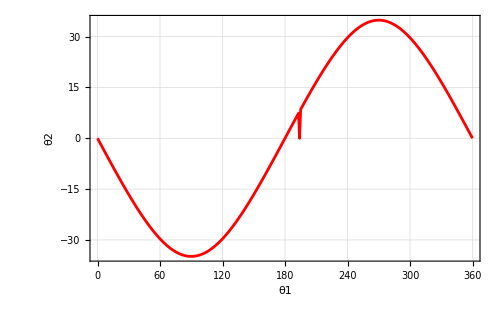

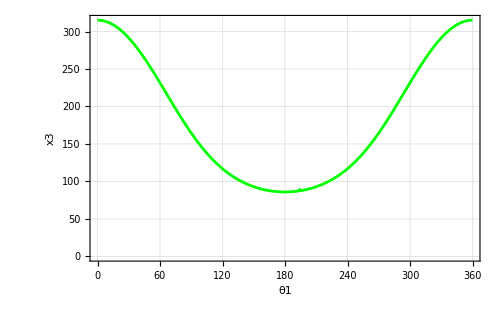

```mathematica
Tabla1=Table[{i,(θ2/.SolPos[i])/Degree}, {i,0,360,1}];  (*la x va a ir de 0 hasta 360 y va ir de 1 en 1*)
Tabla2=Table[{i,(x3/.SolPos[i])/Degree}, {i,0,360,1}];

Fig1 = Grafica [Tabla1,RGBColor[1,0,0],"θ1","θ2"]
Fig2 = Grafica [Tabla2,RGBColor[0,1,0],"θ1","x3"]
(*
ListPlot[Tabla1 ,Joined-> True,PlotStyle->RGBColor[1,0,0],Frame-> True, FrameLabel-> {"θ1","θ2","c","d"},ImageSize->500,GridLines->Automatic] 
(*Dibuja una lista*)
ListPlot[Tabla2,Joined-> True,PlotStyle->RGBColor[0,1,0],Frame-> True, FrameLabel-> {"θ1","x3","c","d"},ImageSize->500,GridLines->Automatic]
*)
```

## Solución de la Velocidad

La solución inicial de la velocidad NO se requiere, ya que el método numérico a usar no la necesita. Sin embargo la calculamos para comprobar nuestras ecuaciones.
1.

```mathematica
Vel/.PosInicial//MatrixForm (*otra forma de ejecutarlo*)
(*se necesita vaciar lo que se calculo anteriormente*)
```

(0.-vx3
0.+2 ω1+3.5 ω2
0.)

#### Velocidad Inicial

```mathematica
Clear[θ1,θ2,x3];
Clear[ω1,ω2,vx3];
Clear[α1,α2,ax3];

θ1=0*Degree; (*Degree= π/180.ba*) (*angulo sugerido de referencia*)
(*FindRoot = Newton-Raphson*)
ω1=2π/1;(*1 revolución en 1 segundo=60RPM*)


VelInicial = Solve[{
Vel[[1]]==0,
Vel[[2]]==0}/.PosInicial,
{ω2,vx3}
]//Flatten
```

{ω2→-3.59039,vx3→0.}

```mathematica
Flatten[{{{{{X,Y}}}}},3]
{{{{{X,Y}}}}}//Flatten (*Para quitar llaves*)
```

{{X,Y}}

{X,Y}

#### Velocidad Total

```mathematica
Clear[θ1,θ2,x3];
Clear[ω1,ω2,vx3];
Clear[α1,α2,ax3];

ω1=2π/1;

For[i=0,i ≤ 360, i+=1, (*ir de 1 en 1 como sugerencia*)
θ1=i*Degree;

(*FindRoot = Newton-Raphson*)

SolVel[i] = Solve[{
Vel[[1]]==0,
Vel[[2]]==0}/.SolPos[i],
{ω2,vx3}]//Flatten
]; (*fin For*)
SolVel[0]
```

{ω2→-3.59039,vx3→0.}

## Gráfica de la Velocidad

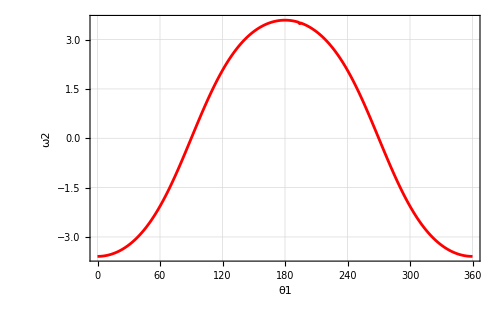

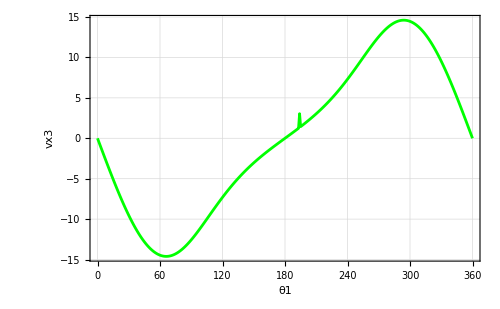

```mathematica
vTabla1=Table[{i,(ω2/.SolVel[i])}, {i,0,360,1}];  (*la x va a ir de 0 hasta 360 y va ir de 1 en 1*)
vTabla2=Table[{i,(vx3/.SolVel[i])}, {i,0,360,1}];

vFig1 = Grafica [vTabla1,RGBColor[1,0,0],"θ1","ω2"]
vFig2 = Grafica [vTabla2,RGBColor[0,1,0],"θ1","vx3"]
```

## Solución de la Aceleración

La solución inicial de la aceleración NO se requiere, ya que el método numérico a usar no la necesita. Sin embargo la calculamos para comprobar nuestras ecuaciones.
1.

```mathematica
Acel/.PosInicial/.VelInicial//MatrixForm
```

(-124.075-ax3
0.+2 α1+3.5 α2
0.)

#### Aceleracion Inicial

```mathematica
Clear[θ1,θ2,x3];
Clear[ω1,ω2,vx3];
Clear[α1,α2,ax3];

θ1=0*Degree; (*Degree= π/180.ba*) (*angulo sugerido de referencia*)
(*FindRoot = Newton-Raphson*)
ω1=2π/1;(*1 revolución en 1 segundo=60RPM*)
α1=0;


AcelInicial = Solve[{
Acel[[1]]==0,
Acel[[2]]==0}/.PosInicial/.VelInicial,
{α2,ax3}
]//Flatten
```

{α2→0.,ax3→-124.075}

#### Aceleración Total

```mathematica
Clear[θ1,θ2,x3];
Clear[ω1,ω2,vx3];
Clear[α1,α2,ax3];

ω1=2π/1;
α1=0;

For[i=0,i ≤ 360, i+=1, (*ir de 1 en 1 como sugerencia*)
θ1=i*Degree;

SolAcel[i] = Solve[{
Acel[[1]]==0,
Acel[[2]]==0}/.SolPos[i]/.SolVel[i],
{α2,ax3}]//Flatten
]; 
SolAcel[0]
```

{α2→0.,ax3→-124.075}

## Gráfica de la Aceleración

```mathematica
aTabla1=Table[{i,(α2/.SolAcel[i])}, {i,0,360,1}];  (*la x va a ir de 0 hasta 360 y va ir de 1 en 1*)
aTabla2=Table[{i,(ax3/.SolAcel[i])}, {i,0,360,1}];

aFig1 = Grafica [vTabla1,RGBColor[1,0,0],"θ1","ω2"]
aFig2 = Grafica [vTabla2,RGBColor[0,1,0],"θ1","vx3"]
```

-Graphics-

-Graphics-

## Animación con Animate

```mathematica
Animate[
θ1=i*Degree;


RR1=T2D[R1];
RR2=T2D[R2];
RR3=T2D[R3];
Cero={0,0};
(*Line[{Cola,Punta}] del vector a graficar*)
Linea1=Line[{Cero,RR1}]/.SolPos[i];
Linea2=Line[{RR1,RR1+RR2}]/.SolPos[i];
p1=RR3+{-0.7,-0.3}; (*Valores para hacer un cuadrado*)
p2=RR3+{0.7,0.3};
Cuadro=Rectangle[p1,p2]/.SolPos[i];

Punto1=Point[Cero]/.SolPos[i];
Punto2=Point[RR1]/.SolPos[i];
Punto3=Point[RR1+RR2]/.SolPos[i];


Barra1=Graphics[{Thickness[0.02],RGBColor[1,0,0],Linea1}];
Barra2=Graphics[{Thickness[0.02],RGBColor[0,0.5,0],Linea2}];
Corredera=Graphics[{RGBColor[0,0,0.5],Cuadro}];
Pernos=Graphics[{PointSize[0.02],Punto1,Punto2,Punto3}];

Show[Barra1,Corredera,Barra2,Pernos,
Frame-> True,PlotRange->{{-2.5,7},{-2.5,2.5}}],{i,0,360,1},AnimationRunning-> False] (*Solo acepta gráficos con la instrucción Graphics*)(*Se adicionan comandos para la animación*)
```

## Animación con For para GIF

```mathematica
For[i=0,i≤360,i+=1, 
θ1=i*Degree;


RR1=T2D[R1];
RR2=T2D[R2];
RR3=T2D[R3];
Cero={0,0};
(*Line[{Cola,Punta}] del vector a graficar*)
Linea1=Line[{Cero,RR1}]/.SolPos[i];
Linea2=Line[{RR1,RR1+RR2}]/.SolPos[i];
p1=RR3+{-0.7,-0.3}; (*Valores para hacer un cuadrado*)
p2=RR3+{0.7,0.3};
Cuadro=Rectangle[p1,p2]/.SolPos[i];

Punto1=Point[Cero]/.SolPos[i];
Punto2=Point[RR1]/.SolPos[i];
Punto3=Point[RR1+RR2]/.SolPos[i];


Barra1=Graphics[{Thickness[0.02],RGBColor[1,0,0],Linea1}];
Barra2=Graphics[{Thickness[0.02],RGBColor[0,0.5,0],Linea2}];
Corredera=Graphics[{RGBColor[0,0,0.5],Cuadro}];
Pernos=Graphics[{PointSize[0.02],Punto1,Punto2,Punto3}];

Simula[i]=Show[Barra1,Corredera,Barra2,Pernos,
Frame-> True,PlotRange->{{-2.5,7},{-2.5,2.5}}]] ;(*Solo acepta gráficos con la instrucción Graphics*)(*Se adiciona comandos para la animación*)
```

## GIF Animado

```mathematica
TablaGif = Table[Simula[i], {i, 0, 360, 10}];
Export["C:\\Users\\CRAUL\\Documents\\Wolfram Mathematica\\Troquel.gif",TablaGif]
```

Export::nodir: Directory C:\Users\CRAUL\Documents\Wolfram Mathematica\ does not exist.

Export::noopen: Cannot open C:\Users\CRAUL\Documents\Wolfram Mathematica\Troquel.gif.

$Failed